{20,20,4}

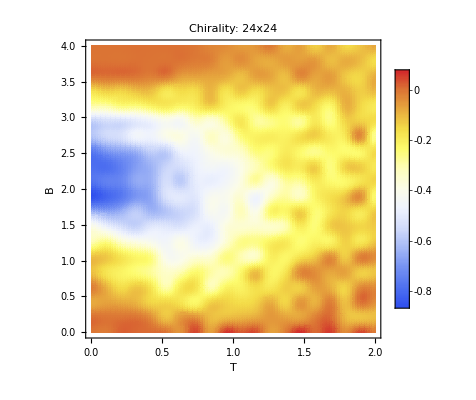

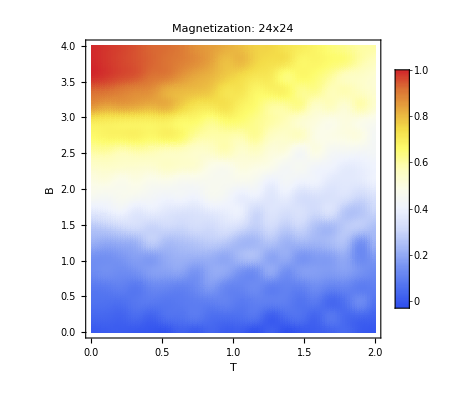

```mathematica
SetDirectory[NotebookDirectory[]];
a=Import["H_label.csv","Data"];
a=ArrayReshape[a,{20,20,4}];
a=Reverse[a,2];
Dimensions[a]
ListDensityPlot[a[[All,All,1]],DataRange->{{0,2},{0,4}},ColorFunction->"TemperatureMap",PlotLabel->Style["Chirality: 24x24",FontSize->20],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->2]
ListDensityPlot[a[[All,All,2]],DataRange->{{2,0},{0,4}},ColorFunction->"TemperatureMap",PlotLabel->Style["Magnetization: 24x24",FontSize->20],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->2]
```

{20,20,4}

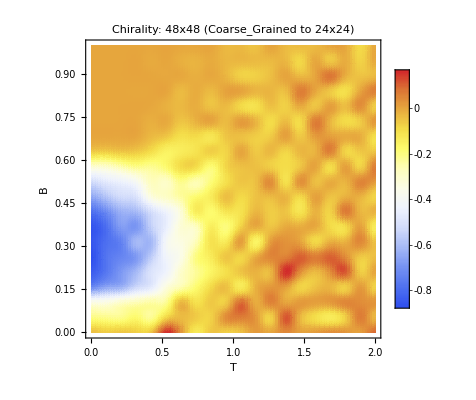

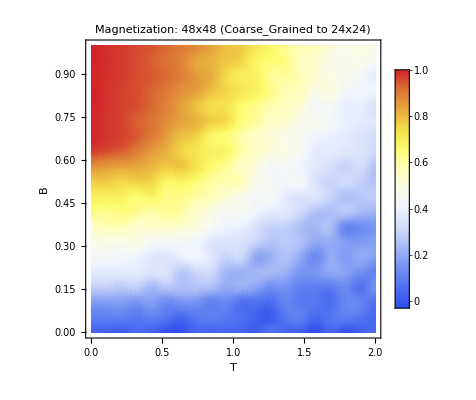

```mathematica
SetDirectory[NotebookDirectory[]];
a=Import["H2CG_label.csv","Data"];
a=ArrayReshape[a,{20,20,4}];
a=Reverse[a,2];
Dimensions[a]
ListDensityPlot[a[[All,All,1]],DataRange->{{0,2},{0,1}},ColorFunction->"TemperatureMap",PlotLabel->Style["Chirality: 48x48 (Coarse_Grained to 24x24)",FontSize->16],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->2,PlotRange->All]
ListDensityPlot[a[[All,All,2]],DataRange->{{2,0},{0,1}},ColorFunction->"TemperatureMap",PlotLabel->Style["Magnetization: 48x48 (Coarse_Grained to 24x24)",FontSize->16],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->2]
```

{20,20,4}

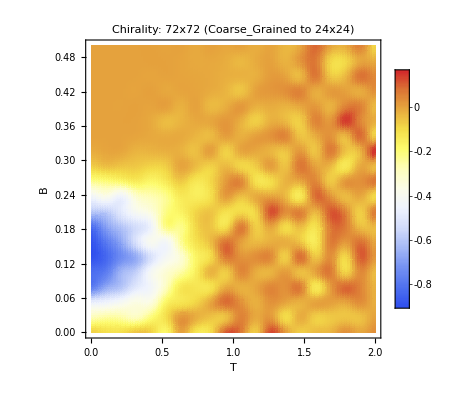

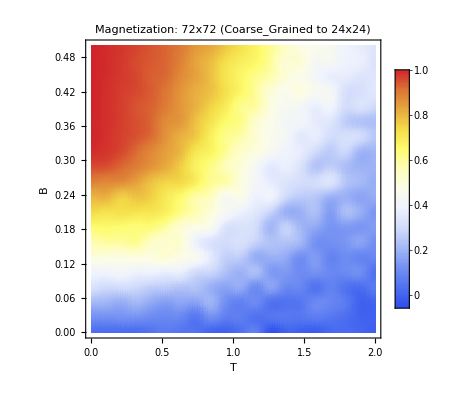

```mathematica
SetDirectory[NotebookDirectory[]];
a=Import["H3CG_label.csv","Data"];
a=ArrayReshape[a,{20,20,4}];
a=Reverse[a,2];
Dimensions[a]
ListDensityPlot[a[[All,All,1]],DataRange->{{0,2},{0,0.5}},ColorFunction->"TemperatureMap",PlotLabel->Style["Chirality: 72x72 (Coarse_Grained to 24x24)",FontSize->16],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->2,PlotRange->All]
ListDensityPlot[a[[All,All,2]],DataRange->{{2,0},{0,0.5}},ColorFunction->"TemperatureMap",PlotLabel->Style["Magnetization: 72x72 (Coarse_Grained to 24x24)",FontSize->16],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->2]
```

{20,20,4}

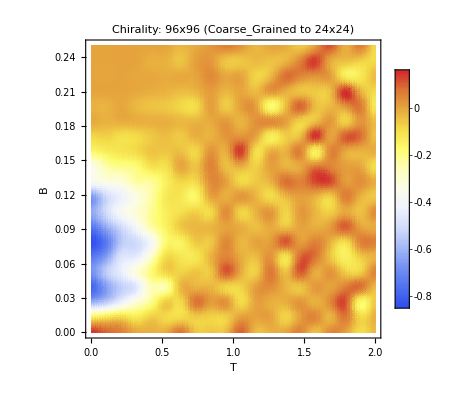

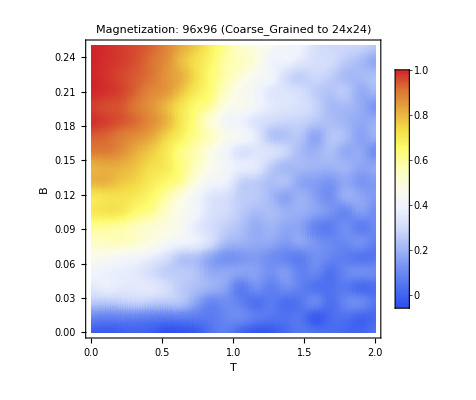

```mathematica
SetDirectory[NotebookDirectory[]];
a=Import["H4CG_label.csv","Data"];
a=ArrayReshape[a,{20,20,4}];
a=Reverse[a,2];
Dimensions[a]
ListDensityPlot[a[[All,All,1]],DataRange->{{0,2},{0,0.25}},ColorFunction->"TemperatureMap",PlotLabel->Style["Chirality: 96x96 (Coarse_Grained to 24x24)",FontSize->16],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->2,PlotRange->All]
ListDensityPlot[a[[All,All,2]],DataRange->{{2,0},{0,0.25}},ColorFunction->"TemperatureMap",PlotLabel->Style["Magnetization: 96x96 (Coarse_Grained to 24x24)",FontSize->16],PlotLegends->Automatic,FrameLabel->{Style[T,FontSize->16],Style[B,FontSize->16]},InterpolationOrder->2]
```